Interpolation with DTFT and IDTFT

```mathematica
N cp=33;(*the number of controlled points*)
```

```mathematica
h[n_]:=If[n==(N cp-1)/2,α,α*Sin[((N cp-1)/2-n)*α*Pi]/(((N cp-1)/2-n)*α*Pi)]/.α->4/10
```

```mathematica
h[n]
```

If[n==16,2/5,(2 Sin[1/5 ((N cp-1)/2-n) 2 π])/(5/5 (((N cp-1)/2-n) 2 π))]

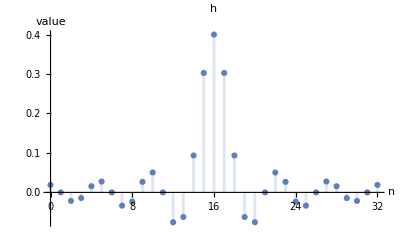

```mathematica
plt h=DiscretePlot[h[n],{n,0,N cp-1},PlotRange->Full,AxesLabel->{"n","value"},PlotLabel->"h"]
```

```mathematica
H[Ω_]=Sum[h[n]*Exp[-I*Ω*n],{n,0,N cp-1}];
```

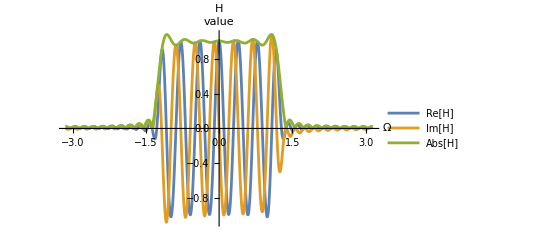

```mathematica
Plot[{Re[H[Ω]],Im[H[Ω]],Abs[H[Ω]]},{Ω,-Pi,Pi},AxesLabel->{"Ω","value"},PlotLegends->{"Re[H]","Im[H]","Abs[H]"},PlotLabel->"H"]
```

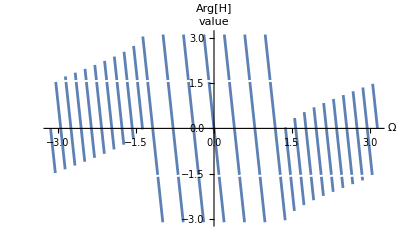

```mathematica
Plot[Arg[H[Ω]],{Ω,-Pi,Pi},AxesLabel->{"Ω","value"},PlotLabel->"Arg[H]"]
```

```mathematica
h̃[t_]=Integrate[H[Ω]*Exp[I*Ω*t],{Ω,-Pi,Pi}]/(2Pi);
```

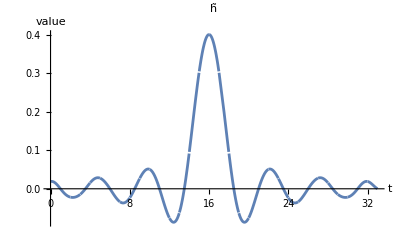

```mathematica
plt th=Plot[h̃[t],{t,0,N cp},PlotRange->Full,AxesLabel->{"t","value"},PlotLabel->"h̃"]
```

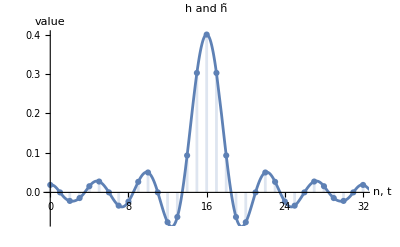

```mathematica
Show[plt h,plt th,PlotLabel->"h and h̃",AxesLabel->{"n, t","value"}]
```

```mathematica
SuperDagger[h][d_,n_]=h̃[n-d];
```

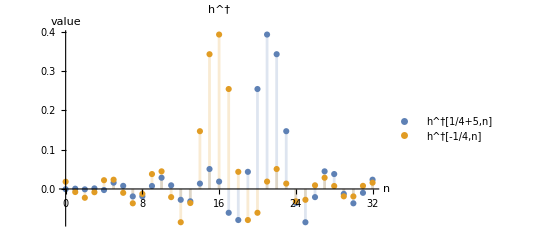

```mathematica
plt hdg=DiscretePlot[{SuperDagger[h][1/4+5,n],SuperDagger[h][-1/4,n]},{n,0,N cp-1},PlotRange->Full,AxesLabel->{"n","value"},PlotLabel->"h^†",PlotLegends->{"h^†[1/4+5,n]","h^†[-1/4,n]"}]
```